```mathematica
ClearAll["Global`*"];
```

```mathematica
ϵ=10^(-3);znak=3;

X0={-1,-2};α=1;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2

X0={1,-1};g[{x_,y_}]:=2(x-1)^2+y^2-1

(*X0={-1,-2};g[{x_,y_}]:=-5+(29 x^2)/12+(5 y^2)/4-√2 x y*)
(*g[{x_,y_}]:=(x-1/2)^3-y(*тестовый пример для данного метода*)*)
(*g[{x_,y_}]:=x+y^2-2y*)
(*X0={1,-1};g[{x_,y_}]:=2(x-1)^2+y^2-1(*доп пример*)*)
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
X=X0;
points={X0};
vspom={X0};
norm=NormGradF[X0];
fValues={f[X0]};
i=0;

While[NormGradF[X]>ϵ,

w=antiGradF[X];i+=3;
θ=NArgMin[f[X+κ w],κ,StepMonitor:>i++];
X+=θ w;
vspom=Append[vspom,X];
If[g[X]>0,X=NArgMin[{Norm[{x,y}-X],g[{x,y}]≤0},{x,y}];vspom=Append[vspom,X];];
points=Append[points,X];
fValues=Append[fValues,f[X]];i++;
];"Результат получен за "<>ToString[Length[points]-1]<> " итер. Точка минимума X = "<>ToString[SetAccuracy[X,znak]]<>". Функция f(x) в алгоритме была вычислена "<>ToString[i]<>" раз."
SetAccuracy[f[X],znak]" - минимум функции f(X)"
```

Результат получен за 57 итер. Точка минимума X = {1.0, 1.0}. Функция f(x) в алгоритме была вычислена 3350 раз.

0.  - минимум функции f(X)

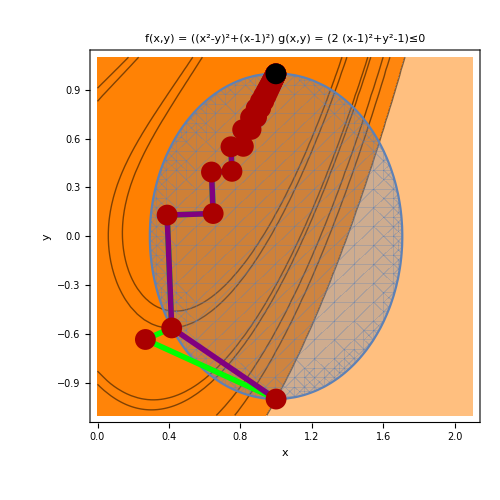

```mathematica
CP0={0,-1.1}; CP1={2.1,1.1};
(*CP0={-2.1,-2.1}; CP1={2.1,2.1};*)
(*CP0={0,-1.1}; CP1={2.1,1.1};(*доп пример*)*)
 a:=Length[points]-1;b:=Length[points];
Show[ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),5]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;2]]~Join~{fValues[[a]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Column[{Text[Style["f(x,y) = ",Italic]f[{x,y}]],Text[Style["g(x,y) = ",Italic]g[{x,y}]≤0]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Green,Thickness[0.008],Line[vspom],Purple,Thickness[0.008],Line[points],Darker[Red],PointSize[0.03],Point[vspom],Black,Point[points[[Length[points]]]]}],RegionPlot[g[{x,y}]≤0,{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]}]]
```